```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1.24×10^6,87,2.74×10^9,3.35×10^9,16000181,26,0,0}

{459203,16}

```mathematica
nullpos=Position[datafull[[All,9]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
(* mostlyzeropos=Position[datafull[[All,9]],_?(#==0&)][[{2,3}]];
datafull=Delete[datafull,mostlyzeropos]; *)
```

```mathematica
deletepos=Position[datafull[[All,10]],_?(5*10^7<#&)];
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos2=Position[datafull[[All,9]],_?(10^9<#&)];
datafull=Delete[datafull,deletepos2];
```

```mathematica
datafull[[Flatten@Position[datafull[[All,9]],_?(500000<#&)],9]]/=1000;
```

```mathematica
datafull=datafull[[Flatten@Position[datafull[[All,10]],_?(0≠#&)]]];
```

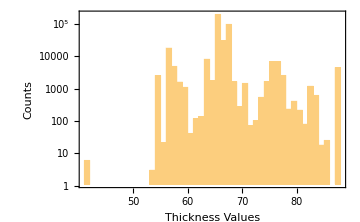
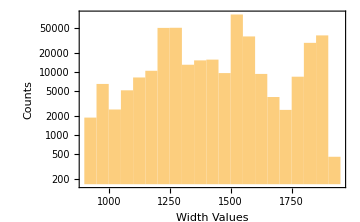

```mathematica
{Histogram[datafull[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,10]];
widthvaluesthkpos=datafull[[All,9]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|-0.0003581→6,0.→7,7.37584×10^-14→8,7.40346×10^-14→8,7.42935×10^-14→6,7.44644×10^-14→7,17479,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]];
```

```mathematica
thickvaluesthkpos=datafull[[All,10]];
widthvaluesthkpos=datafull[[All,9]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

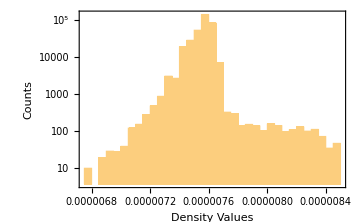

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
Length@datafull
```

348291

```mathematica
datafull[[1]]
```

{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1240.,87,2.74×10^9,3.35×10^9,16000181,26,0,0}

```mathematica
(* Sort[datafull,#1[[2]]<#2[[2]]&]==Sort[datafull,AbsoluteTime[{#[[5]],{"Day","Month","YearShort"}}]&] *)
```

```mathematica
datafullsorted=Sort[datafull,#1[[2]]<#2[[2]]&];
```

```mathematica
(* checking if sequences are revealing consecutive *)
Length@Table[DeleteDuplicates@i,{i,Split[datafullsorted[[All,1]],#2==#1&]}]
Length@DeleteDuplicates[datafullsorted[[All,1]]]
```

348291

348291

Deletion of sequences less than 50

```mathematica
deletepos3=Flatten@Table[Position[datafullsorted[[All,2]],i],{i,Keys@Cases[Normal@Counts@datafullsorted[[All,2]],_?(Values[#]<50&)]}];
datafullsorted=Delete[datafullsorted,Partition[deletepos3,1]];
```

```mathematica
datafullsorted[[1000]]
```

{8470,181,118123,CCM1,04.01.17,17000721-02,150867,#NAME?,1290.,65,2.07×10^9,3.25×10^9,17000721,26,0,0}

```mathematica
Dimensions@datafullsorted
```

{347418,16}

```mathematica
(* Export["ccm_manipulated_347418.csv",datafullsorted] *)
```